```mathematica
<<ASTRAINterpret`
```

```mathematica
SetDirectory["C:\\Users\\jkj62\\Documents\\GitHub\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\Ultrashort\\MOGA\\"]
```

C:\Users\jkj62\Documents\GitHub\OnlineModel\SimulationFramework\Examples\CLARA\Ultrashort\MOGA

## Solutions Analysis

```mathematica
iterationnumber=0;
```

```mathematica
fitdata=Select[ImportString[StringJoin@@(#<>"\n"&/@StringTrim[ReadList["best_solutions_running.csv",Record,RecordSeparators->{"\n"}]]),"CSV"],Length[#]>0&];
iterationnumber=fitdata[[Ordering[fitdata,1,#1[[-5]]/#1[[-4]]<#2[[-5]]/#2[[-4]]&],-2]][[1]]
```

444.

```mathematica
iterationdir="iteration_"<>ToString[iterationnumber]<>"\\";
```

## Twiss Analysis

```mathematica
ASTRAemitInterpret[iterationdir<>#<>".Zemit.001"&/@Select[{"injector400","S02","L02","S03","L03","S04","L4H","S05","VBC","S06","L04","S07"},FileExistsQ[iterationdir<>#<>".Zemit.001"]&],ASTRAVerbose->False]
```

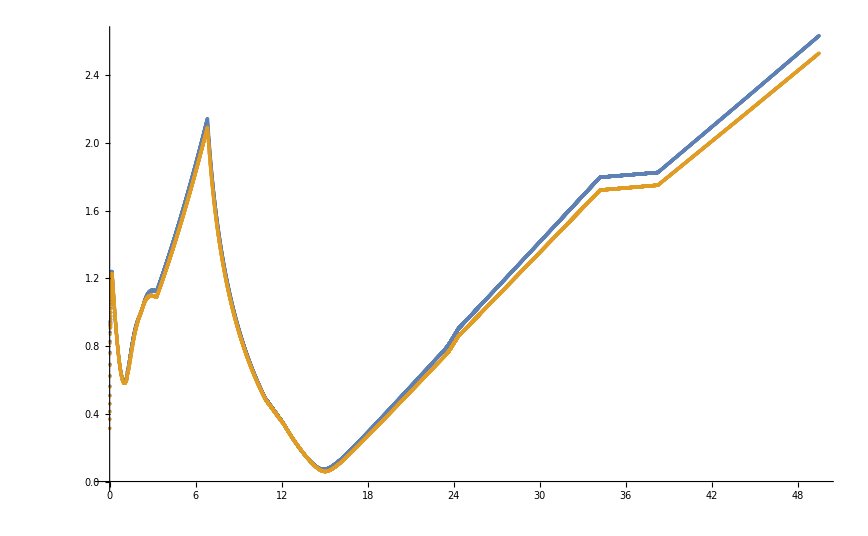

```mathematica
ListPlot[{Transpose[{z[[1;;Length[xrms]]],xrms}],Transpose[{z[[1;;Length[yrms]]],yrms}]},PlotRange->{All,{0,All}}]
```

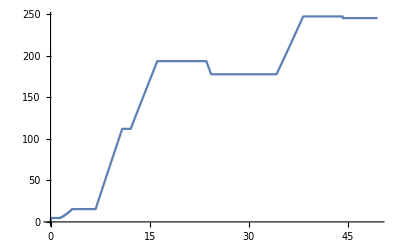

```mathematica
ListLinePlot[{Transpose[{z,Ekin}]},PlotRange->All]
```

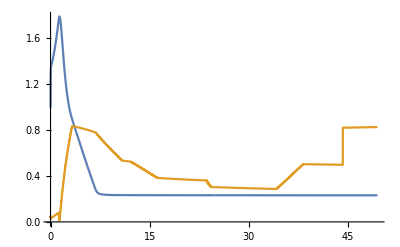

```mathematica
ListLinePlot[{Transpose[{z,10^12(zrms/(1000*3 10^8))}],Transpose[{z,ΔErms/1000}]},PlotRange->All]
```

## Beam Analysis

```mathematica
ASTRABeamInterpret[iterationdir<>"S07.4948.001",ASTRAVerbose->False]
```

```mathematica
t=(z-Mean[z])/QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"]]];
```

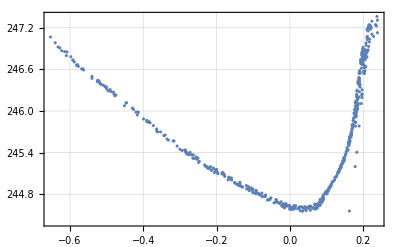

```mathematica
ListPlot[Transpose[{10^12(t-Mean[t]),pz/10^6}],PlotTheme->"Detailed",Axes->True]
```

```mathematica
slicelength=10^12(Max[t]-Min[t])/16;
$CHARGE=250;
```

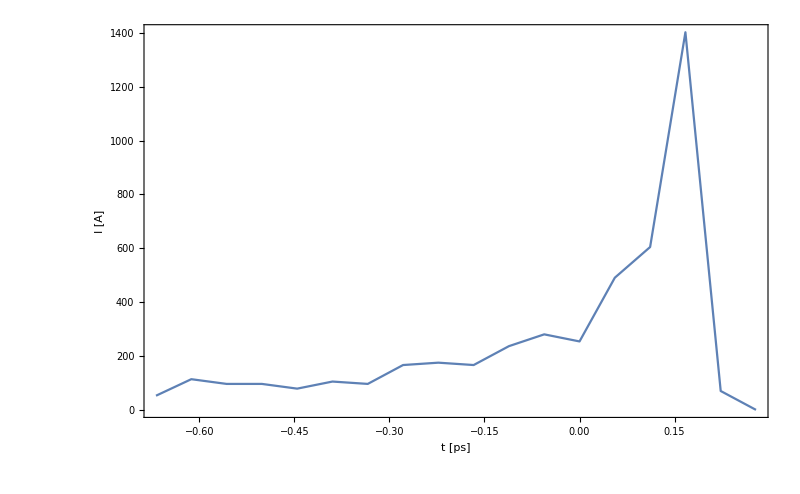

```mathematica
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,elsplotstyle,Frame->True,PlotRange->All,FrameLabel->{"t [ps]","I [A]"}]&[{1,250/(slicelength Length[t])}HistogramList[#,{slicelength}]&[10^12(t-Mean[t])]]
```

```mathematica
tn=10^12(t-Mean[t]);
```

```mathematica
FWHM[data_,frac_:2]:=Block[{x,y,max},
{x,y}=Transpose[data];
If[frac<1,
max=Max[y]*frac,
max=Max[y]/frac];
tf=Transpose[{x,Map[#>max&,y]}];
{Position[tf,True][[{1,-1},1]],
Differences[Select[tf,#[[2]]==True&][[{1,-1}]]][[1,1]]}
]
```

```mathematica
bw=RootMeanSquare[tn]/10;
```

```mathematica
SKcurrentDist=SmoothKernelDistribution[tn,bw];
```

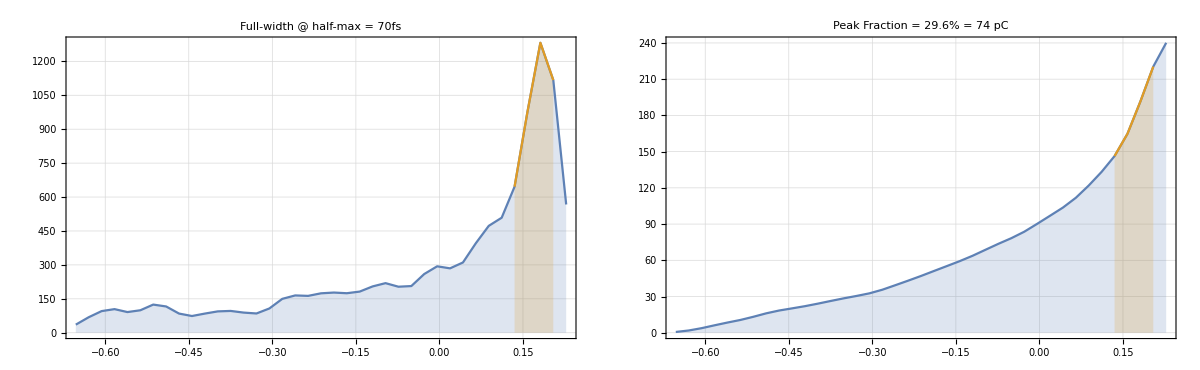

0.210819

```mathematica
{fwhmpos,fwhm}=FWHM[Table[{x,PDF[SKcurrentDist,x]},{x,Min[tn],Max[tn],bw}],2];
{fwqmpos,fwqm}=FWHM[Table[{x,PDF[SKcurrentDist,x]},{x,Min[tn],Max[tn],bw}],2];
pdfdata=Table[{x, PDF[SKcurrentDist,x]},{x,Min[tn],Max[tn],bw}];
cdfdata=Table[{x,100 CDF[SKcurrentDist,x]},{x,Min[tn],Max[tn],bw}];
GraphicsRow[{ListLinePlot[{{1,250}#&/@pdfdata,{1,250}#&/@Take[pdfdata,fwhmpos]},Filling->Bottom,PlotRange->All,PlotLabel->"Full-width @ half-max = "<>ToString[Round[10^3 fwhm,1]]<>"fs",PlotTheme->"Detailed"],ListLinePlot[{{1,250/100}#&/@cdfdata,{1,250/100}#&/@Take[cdfdata,fwhmpos]},Filling->Bottom,PlotRange->All,PlotLabel->"Peak Fraction = "<>ToString[Round[Differences[Take[cdfdata,fwhmpos][[{1,-1},2]]][[1]],0.1]]<>"% = "<>ToString[Round[250/100 Differences[Take[cdfdata,fwhmpos][[{1,-1},2]]][[1]],1]]<>" pC",PlotTheme->"Detailed"]},ImageSize->1200,Spacings->0]
StandardDeviation[Take[pdfdata,fwhmpos][[All,2]]]/Max[pdfdata[[All,2]]]
(*Export["C:\\Users\\jkj62\\Pictures\\FEBE\\5kA\\FWHM.png",%,ImageResolution->200]*)
```

## HOF

```mathematica
Clear[readInData];
```

```mathematica
readInData[]:=Block[{},
Print["Updating d"];
d=Select[ImportString[StringJoin@@(#<>"\n"&/@StringTrim[ReadList["best_solutions_running.csv",Record,RecordSeparators->{"\n"}]]),"CSV"],Length[#]>0&];
If[FileExistsQ["./CLARA_HOF_longitudinal_Genesis_DCP.csv"],
d2=Split[Select[ImportString[StringJoin@@(#<>"\n"&/@StringTrim[ReadList["./CLARA_HOF_longitudinal_Genesis_DCP.csv",Record,RecordSeparators->{"\n"}]]),"CSV"],Length[#]>0&],#1[[-2]]==#2[[-2]]&];
dataHOF=Block[{hof=#},Sort[Select[d,MemberQ[hof[[All,14]],#[[-2]]]&],#1[[-1]]<#2[[-1]]&]]&/@d2;
];
];
```

```mathematica
data=readInData[];
```

Updating d

```mathematica
inputvalues=d[[All,1;;15]];
{espread,peakI,Xmax}=Transpose[d[[All,16;;18]]];
id=d[[All,-2]];
fitness=d[[All,-1]];
```

```mathematica
inputvaluesHOF=Block[{hof=#},Select[Transpose[{espread,peakI,Xmax,id}],MemberQ[hof[[All,-1]],IntegerPart[#[[-1]]]]&]]&/@d2;
```

```mathematica
Length/@d2
```

{7,19,31,47,55,67,77,92,100,110,117,116,125,131,138,150,148,152,161,153,160,168,172,174,168,170,174,171,162,165,173,172,171}

```mathematica
ListLogLinearPlot[Select[Select[#,#[[1]]>0&][[All,{2,1}]]&/@inputvaluesHOF,Length[#]>0&],PlotRange->{{50,5000},{0,1.5}},PlotTheme->"Detailed",GridLines->{Range[0,5000,250],Range[0,2,0.1]},PlotStyle->{PointSize[0.01]},Epilog->{Red(*,Line[Sort[{Log[#[[1]]],#[[2]]}&/@inputvaluesHOF[[-1,All,{1,2}]]]],*),Opacity[0.5],Thickness[0.01],BSplineCurve[{Log[#[[1]]],#[[2]]}&/@Sort[{{115,0.17},{125,0.16},{500,0.2},{1100,0.28},{2000,0.46},{2150,0.5},{2350,1.1}}],SplineDegree->4]},Prolog->{GrayLevel[0.1],Opacity[0.2],Thickness[0.001],Point[{Log[#[[1]]],#[[2]]}]&/@Select[Transpose[{espread,peakI,Xmax,id}],#[[1]]>0&][[All,{1,2}]]},BaseStyle->{FontSize->16},ImageSize->800,FrameLabel->{"Peak Current [A]","Energy Spread [%]"}]
(*Export["C:\\Users\\jkj62\\Pictures\\XARA\\MOGA\\ParetoFront 2 Zoom.png",%,ImageResolution->200]*)
```

-Graphics-

```mathematica
ListPlot[Select[Select[#,#[[1]]>0&][[All,{2,1}]]&/@inputvaluesHOF,Length[#]>0&],PlotRange->{{50,2500},{0,1.5}},PlotTheme->"Detailed",GridLines->{Range[0,5000,250],Range[0,2,0.1]},PlotStyle->{PointSize[0.01]},Epilog->{Red(*,Line[Sort[{Log[#[[1]]],#[[2]]}&/@inputvaluesHOF[[-1,All,{1,2}]]]],*),Opacity[0.5],Thickness[0.01],BSplineCurve[{#[[1]],#[[2]]}&/@Sort[{{115,0.17},{125,0.16},{500,0.2},{1100,0.28},{2000,0.46},{2120,0.5},{2340,1.1}}],SplineDegree->4]},Prolog->{GrayLevel[0.1],Opacity[0.2],Thickness[0.001],Point[{Log[#[[1]]],#[[2]]}]&/@Select[Transpose[{espread,peakI,Xmax,id}],#[[1]]>0&][[All,{1,2}]]},BaseStyle->{FontSize->16},ImageSize->800,FrameLabel->{"Peak Current [A]","Energy Spread [%]"}]
(*Export["C:\\Users\\jkj62\\Pictures\\XARA\\MOGA\\ParetoFront 2 Zoom.png",%,ImageResolution->200]*)
```

-Graphics-